```mathematica
MinDiffMod[x_,y_,p_]:=Min[#,p-#]&@Mod[x-y,p]
```

```mathematica
HarmonicGrowth[x_]:=(3/4)(1-1/(x+1))
```

```mathematica
Options[Hexagon]={ColorFunction->(Which[#==0,Black,#==1,White,#>=2,Hue@HarmonicGrowth[#-2]]&),InsetColorFunction->Which[#==0,White,#==1,Black,#>=2,Hue[HarmonicGrowth[#-2]+1/2]]&,
InsetStyle->{FontFamily->"Georgia"},
EdgeFormFunction->(If[#==1,EdgeForm[Black],Nothing]&)};
```

```mathematica
Hexagon[n_Integer?NonNegative,{{x_,y_}},opts:OptionsPattern[]]:=
GraphicsGroup[{
OptionValue[ColorFunction][n],
OptionValue[EdgeFormFunction][n],
Polygon[CirclePoints[{1,Pi/2},6]+{x,y}],Inset[Text[Style[n,Flatten[{OptionValue[InsetColorFunction][n],OptionValue[InsetStyle]}]]](*,{x,y},Scaled[{0.5,0.5}]*)]}]
```

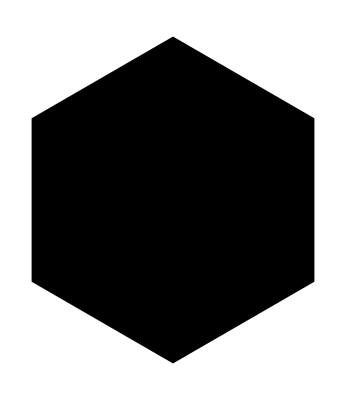

```mathematica
Polygon@CirclePoints[{1,Pi/2},6]//Graphics
```

```mathematica
HexPoints=CirclePoints[{1,Pi/2},6];
```

```mathematica
{TopLeftCorner,InitialTopRowPoint0,InitialTopRowPoint1,InitialLowerFrontPoint}=HexPoints[[{2,1,-1,3}]];
```

```mathematica
LowerPoints=HexPoints[[-3;;-2]];
```

```mathematica
HorizontalDifferenceVector=HexPoints//(#[[-1]]+#[[-2]]&);
```

```mathematica
LowerDifferenceVector=HexPoints//(#[[-2]]+#[[-3]]&);
```

```mathematica
Block[{n,k},VectorTo[{n_,k_}]=n HorizontalDifferenceVector+k LowerDifferenceVector]
```

{(√3 k)/2+√3 n,-(3 k)/2}

Each non-boundary hexagon introduces two new points (note that each vertex is shared by 3 hexagons, and 6/3 = 2). As we expand, though, we still need to introduce boundary points. Still...we know the shape we’re going to create in advance. It’s a set of points. Why not let the computer worry about the code by using actual indices of lattice coordinates?

So. We generate a list of integer pairs, {x,y}, encoding the position of the hexagon via integers. The actual position of the center is of the form x * horizontalDifferenceVector + y * LowerDifferenceVector.

Each point introduces some number of coordinate points. Our task: given any lattice point, find the other lattice points which share coordinate points with it (and which). We also need to do this in order, so that the polygon actually "goes the right way". We'll choose counterclockwise. So we start with the 2 points {n, k} introduces. Then we need the top right point, which comes from the first point of the {n+1, k–1} hexagon. Then the next one is the second point of {n, k–1}, then the first one of that same hexagon. Then the second one of {n-1, k}. So altogether, we want

```mathematica
IndexOf /@ {{{n,k}, 1}, {{n,k}, 2},{{n+1,k-1},1},{{n,k-1},2},{{n,k-1},1},{{n-1,k},2}}
```

{IndexOf[{{n,k},1}],IndexOf[{{n,k},2}],IndexOf[{{1+n,-1+k},1}],IndexOf[{{n,-1+k},2}],IndexOf[{{n,-1+k},1}],IndexOf[{{-1+n,k},2}]}

We should probably encode the boundary points as {{n,k},i} for n or k equal to 0.

We can generate the full list of introduced {{n,k},i}’s from the list of {n,k}’s, then use First /@ PositionIndex[list] to get IndexOf?

We could even just use the “adjacent point list” over which we map IndexOf as a way to generate all the point codes (and then DeleteDuplicates). Each point would be produced three times though. I’d rather just have the points that need to produce extra points. This isn’t too hard, assuming we use a region whose boundary is of an appropriate form. We won’t check that, though.

Note that we need to keep reducing the row length, since we only know the stuff “inside” what we’ve calculated. Effectively, we always have nmax ≥ k

We’ll use {{n,k},0} for the center. That’s fine.

```mathematica
LatticePointRange[n_Integer,k_]:=Join@@Table[{n1,k1},{k1,1,k},{n1,1,n-k1+1}]
```

```mathematica
LatticePointRange[{ni_Integer,nf_Integer},k_]:=Join@@Table[{n1,k1},{k1,1,k},{n1,ni,nf-k1+1}]
```

```mathematica
GeneratePointCodes[{n_,k_},ninit_:1,kinit_:1]:=
{If[n==ninit&&k==kinit,{{ninit,kinit-1},1},Nothing],
If[k==kinit,Splice[{{{n,kinit-1},2},{{n+1,kinit-1},1}}],Nothing],
If[n==ninit,{{ninit-1,k},2},Nothing],
{{n,k},0},{{n,k},1},{{n,k},2}}
```

```mathematica
GeneratePointCodes[{1,1}]
```

{{{1,0},1},{{1,0},2},{{2,0},1},{{0,1},2},{{1,1},0},{{1,1},1},{{1,1},2}}

```mathematica
GenerateAllPointCodes[latticepointlist:{{_,_}...},ninit_:1,kinit_:1]:=Join@@(GeneratePointCodes[#,ninit,kinit]&/@latticepointlist)
```

```mathematica
HexagonPointCodesAt[{n_,k_}]:={{{n,k}, 1}, {{n,k}, 2},{{n+1,k-1},1},{{n,k-1},2},{{n,k-1},1},{{n-1,k},2}}
```

```mathematica
HexagonCoordinates[{{n_,k_},i:1|2}]:=VectorTo[{n,k}]+LowerPoints[[i]]
```

```mathematica
HexagonCoordinates[{{n_,k_},0}]:=VectorTo[{n,k}]
```

```mathematica
Clear[CreateDownwardTiling]
```

```mathematica
CreateDownwardTiling[n_Integer,k_,f_,hexgraphic_]:=Module[{latticepoints=LatticePointRange[n,k],pointcodes,indexOf},
pointcodes=GenerateAllPointCodes[latticepoints];indexOf=First/@PositionIndex[pointcodes];GraphicsComplex[HexagonCoordinates/@pointcodes,hexgraphic[f[#],indexOf/@HexagonPointCodesAt[#],indexOf[{#,0}]]&/@latticepoints]]
```

```mathematica
CreateDownwardTiling[{ni_Integer,nf_Integer},k_,f_,hexgraphic_]:=Module[{latticepoints=LatticePointRange[{ni,nf},k],pointcodes,indexOf},
pointcodes=GenerateAllPointCodes[latticepoints,ni];indexOf=First/@PositionIndex[pointcodes];GraphicsComplex[HexagonCoordinates/@pointcodes,hexgraphic[f[#],indexOf/@HexagonPointCodesAt[#],indexOf[{#,0}]]&/@latticepoints]]
```

```mathematica
G[{n_,1}]:=(G[{n,1}]=Prime[n])
```

```mathematica
G[{n_,k_}]:=(G[{n,k}]=Abs[G[{n,k-1}]-G[{n+1,k-1}]])
```

```mathematica
AbsMod[expr_,n_]:=Min[Mod[#,n],Mod[-#,n]]&@expr
```

```mathematica
Clear[GAbsMod]
```

```mathematica
GAbsMod[m_][{n_,k_}]:=(GAbsMod[m][{n,k}]=AbsMod[G[{n,k}],m])
```

```mathematica
GMod[m_][{n_,k_}]:=(GMod[m][{n,k}]=Mod[G[{n,k}],m])
```

```mathematica
Clear[GMod1]
```

```mathematica
GMod1[m_][{n_,1}]:=(GMod1[m][{n,1}]=Mod[G[{n,1}],m])
```

```mathematica
GMod1[m_][{n_,k_}]:=(GMod1[m][{n,k}]=Mod[Abs[GMod1[m][{n,k-1}]-GMod1[m][{n+1,k-1}]],m])
```

```mathematica
Options[PolygonGraphic]={ColorFunction->(Which[#==0,Black,#==1,White,#>=2,Hue[HarmonicGrowth[#-2],1/GoldenRatio,1]]&),InsetColorFunction->(Which[#==0,White,#==1,Black,#>=2,Hue[HarmonicGrowth[#-2]+1/2]]&),
InsetStyle->{FontFamily->"Helvetica",Tiny},
EdgeFormFunction->(If[#==1,EdgeForm[Black],Nothing]&),
Text->True};
```

```mathematica
PolygonGraphic[val_,polypoints_List,textpoint_,OptionsPattern[]]:=
GraphicsGroup[{
OptionValue[ColorFunction][val],
OptionValue[EdgeFormFunction][val],
Polygon[polypoints],If[OptionValue[Text],Inset[Text[Style[val,Flatten[{OptionValue[InsetColorFunction][val],OptionValue[InsetStyle]}]]],textpoint,Center],Nothing]}]
```

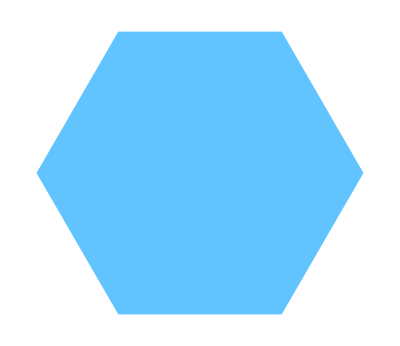

```mathematica
PolygonGraphic[5,CirclePoints[6],{0,0}]//Graphics
```

```mathematica
GeneratePointCodes[{40,1},40]
```

{{{40,0},1},{{40,0},2},{{41,0},1},{{39,1},2},{{40,1},0},{{40,1},1},{{40,1},2}}

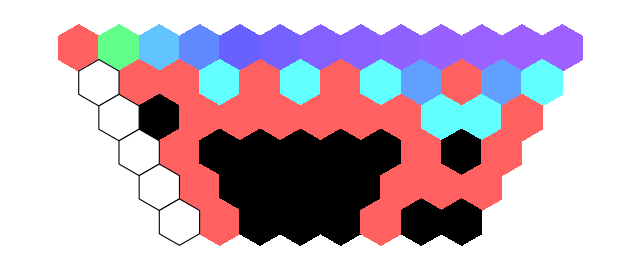

```mathematica
CreateDownwardTiling[13,6,G,PolygonGraphic[##,InsetStyle->{FontFamily->"Helvetica",Large}]&]//Graphics
```

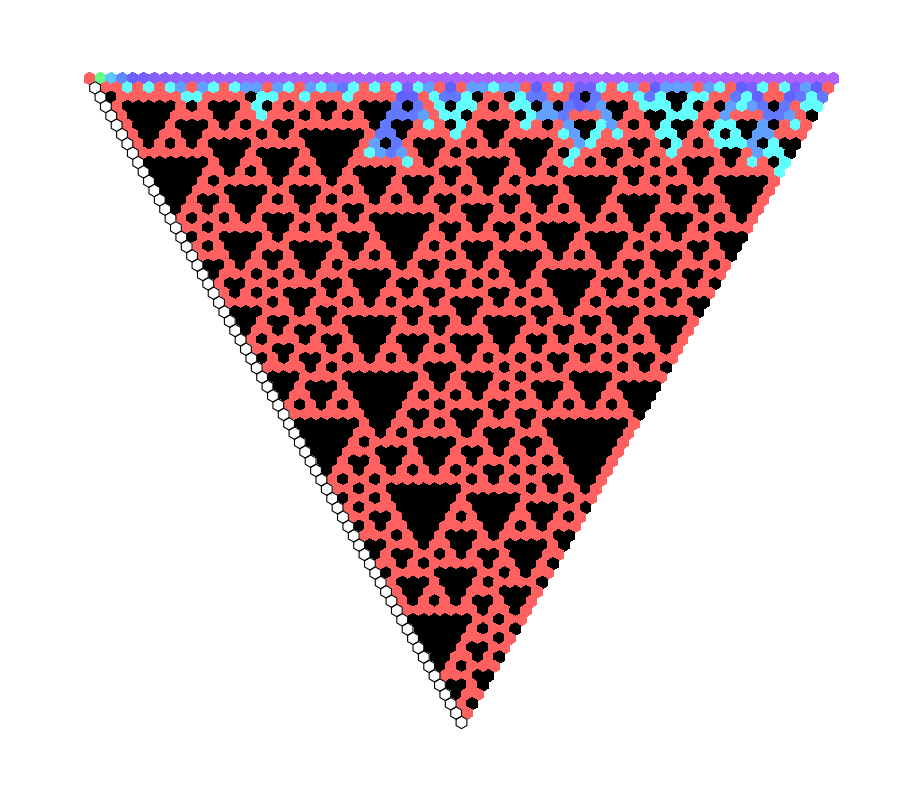

```mathematica
CreateDownwardTiling[70,70,G,PolygonGraphic[##,Text->False]&]//Graphics
```

```mathematica
G[]
```

G[]

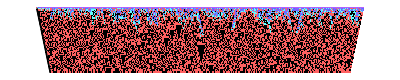

```mathematica
CreateDownwardTiling[600,50,G,PolygonGraphic[##,Text->False]&]//Graphics
```

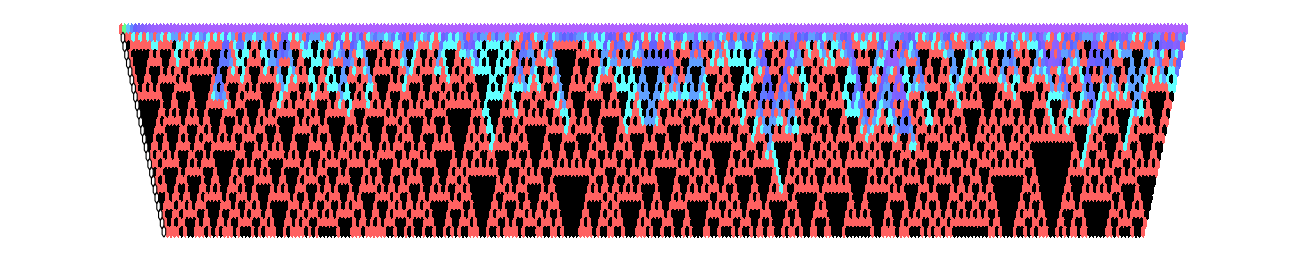

```mathematica
CreateDownwardTiling[300,25,G,PolygonGraphic[##,Text->False]&]//Graphics
```

```mathematica
ApparentHeight[n_,kmax_]:=(ApparentHeight[n,kmax]=If[n==1,0,Catch[Do[If[G[{n,k}]>2,Throw[k]],{k,kmax,1,-1}]]])
```

```mathematica
MaxRecords[list_]:=FoldList[Max,list]
```

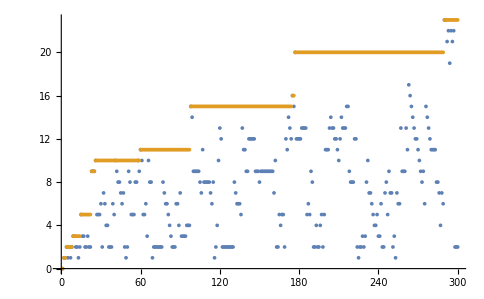

```mathematica
ListPlot[{#,MaxRecords[#]}&@Table[ApparentHeight[n,25],{n,1,300}]]
```

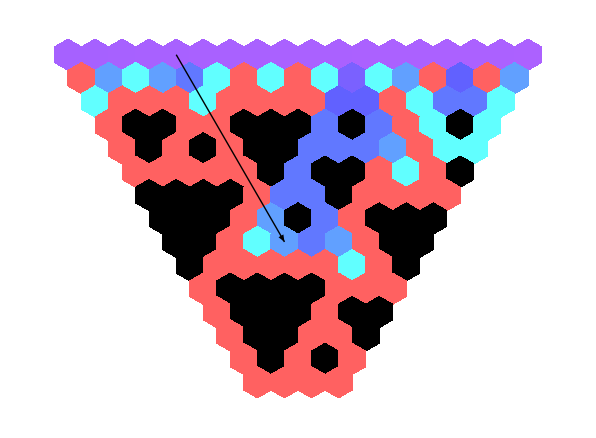

```mathematica
Show[CreateDownwardTiling[{20,37},15,G,PolygonGraphic[##,Text->False]&]//Graphics,Graphics[{Black,Thick,EdgeForm[Black],Arrow[{24HorizontalDifferenceVector+LowerDifferenceVector,24HorizontalDifferenceVector+9LowerDifferenceVector}]}]]
```

```mathematica
(* With[{nmax=500000},ListPlot[{Table[E^2 n^(1/4),{n,1,nmax}],initialdata=MaxRecords[Table[ApparentHeight[n,200],{n,1,nmax}]]}]] *)
```

Could also have just done the following with FirstPosition now that I think about it...wow.

```mathematica
(* initialdata500000=MaxRecords[Table[ApparentHeight[n,200],{n,1,500000}]]; *)
```

```mathematica
(* initialdata750000=MaxRecords[Table[ApparentHeight[n,250],{n,500001,750000}]]; *)
```

There’s definitely a way to compute things here that’s 1) more efficient/iterative instead of recursive 2) only computes up to an encounter with a 0 or 2, *unless it needs to be extended*. We could also potentially just compute up to the bound height, lol. But that’s still rather expensive most of the time.

```mathematica
(* recordPoints=Transpose@MapAt[(#+1)&@*Prepend[0]@*Most@*Accumulate,{1}]@Transpose[{Length[#],First[#]}&/@Split[MaxRecords[Table[ApparentHeight[n,200],{n,1,500000}]]]]; *)
```

```mathematica
(* recordPoints2=Transpose@MapAt[(#+1)&@*Prepend[0]@*Most@*Accumulate,{1}]@Transpose[{Length[#],First[#]}&/@Split[MaxRecords@Join[initialdata500000,initialdata750000]]];*)
```

```mathematica
metadata=<|
"GilbreathRecordPoints500000"->"Computed to a check depth of 200.",
"GilbreathRecordPoints750000"->"Computed the first 500k to a depth of 200, and the next 250k to a depth of 250.",
"GilbreathApparentHeights750000"->"Computed the first 500k to a depth of 200, and the next 250k to a depth of 250."
|>;
```

```mathematica
recordPoints=PersistentSymbol["GilbreathRecordPoints750000","Local"];
```

```mathematica
MapIndexed[(ApparentHeight[First@#2]=#1;)&,PersistentSymbol["GilbreathApparentHeights750000","Local"]];
```

```mathematica
recordPoints[[-20;;-1]]
```

{{4205,57},{5941,65},{23264,69},{31498,73},{31527,81},{31532,87},{31534,95},{92621,97},{103962,111},{141708,113},{271619,126},{271622,127},{325091,129},{325098,131},{515908,132},{515909,135},{733566,137},{733569,139},{733576,144},{733577,147}}

```mathematica
ListPlot[Table[ApparentHeight[n],{n,1,500000}],PlotRange->All]
```

-Graphics-

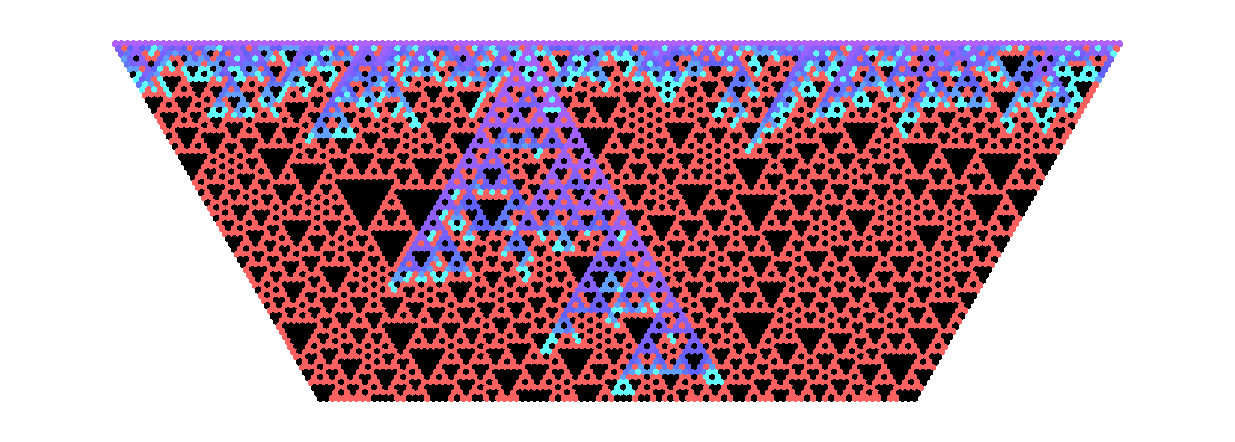

```mathematica
CreateDownwardTiling[{23264-50,23264+69+50},70,G,PolygonGraphic[##,Text->False]&]//Graphics
```

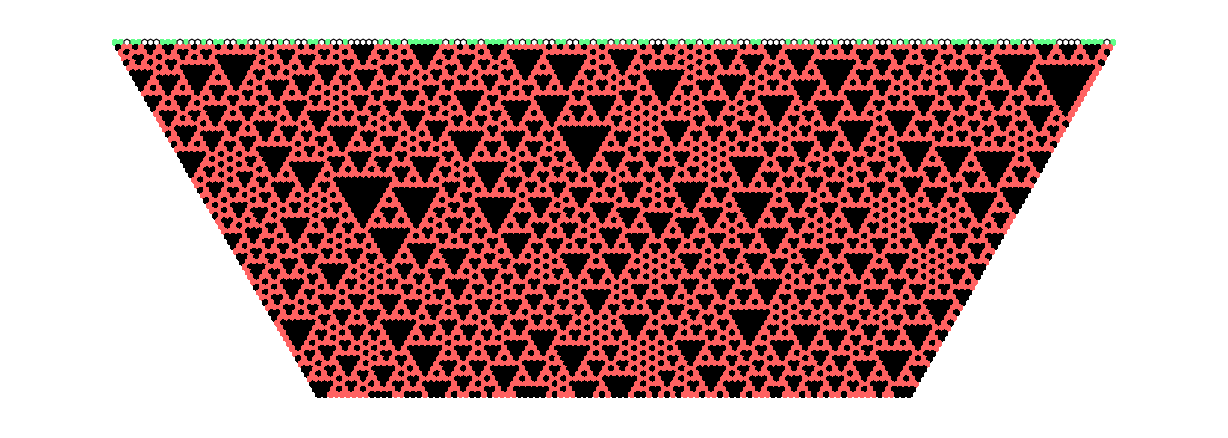

```mathematica
CreateDownwardTiling[{23264-50,23264+69+50},70,GMod[4],PolygonGraphic[##,Text->False]&]//Graphics
```

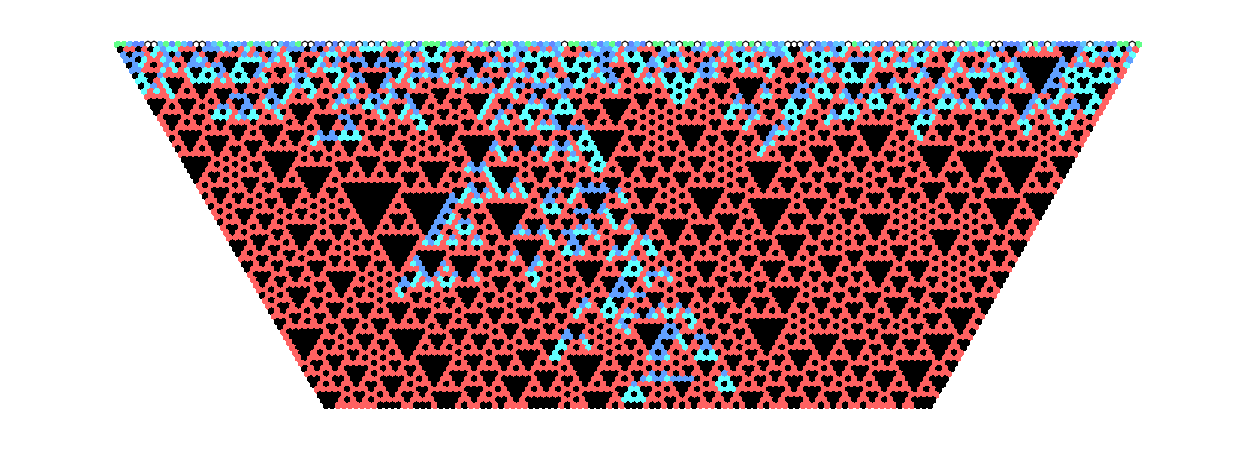

```mathematica
CreateDownwardTiling[{23264-50,23264+69+50},70,GMod[8],PolygonGraphic[##,Text->False]&]//Graphics
```

```mathematica
40330./Norm@HorizontalDifferenceVector
```

23284.5

```mathematica
G[{23283,1}]
```

265621

```mathematica
G[{23284,1}]
```

265703

```mathematica
Differences@Table[G[{n,1}],{n,23220,23300}]
```

{4,6,20,12,18,10,2,16,14,6,6,4,14,16,42,12,2,24,6,6,12,10,6,6,6,24,14,24,10,6,2,12,10,2,4,36,20,4,2,42,18,4,14,6,4,24,8,12,12,10,18,2,28,2,4,14,6,4,8,28,6,6,2,82,6,2,6,12,10,8,10,24,6,20,6,6,12,10,6,14}

Could be interesting not to mod values, but to threshold them. Bring 0 further up or infinity further down, so to speak.

note how whether the purple triangles spawn at a collision of triangle legs depends on the symmetry of the row above the base of the triangle above it, but even if that triangle was not subject to symmetric growth on either side, this can still cause a symmetric row below it, depending on where the asymmetry occurs; a 020 along the base represents a “step” from one side to the other caused by being subject to a 2 on one side and a 0 on the other side at some point. At *which* point matters I think. It also affects the central hole of these length-4 triangles. So can we think of this recursively and match up behavior between different levels? With bigger and bigger “voids” affecting the behavior of its boundary and therefore the potential creation of even bigger voids? Interesting also are the little mostly-cyan (4) tendrils that don’t manage to be triangles.

I wonder if we can make a proof like: ok, if a certain frontier becomes all 4’s, we’re good. If it’s all 6’s or lower on some inner frontier, then we get 4’s, and therefore we’re good. If it’s all 8’s or lower on some region within that, then we get 6’s or lower, and... etc. A bit hard with zeros around though. So really we also want to show that 2’s DO happen eventually. on the interface, lest something shoot through an empty 0 void straight to the 1-rim. 2’s and 0’s are not interchangeable. 2’s are responsible for “digesting”/”breaking down” the larger numbers! We have to know there are enough of them around. I wonder if: we can show that we not only get to a 2-0 realm, but that we produce enough 2’s going rightward, and show some sort of “conservation law” that means we have enough 2’s going rightward from that. Or more that...if we *vary* the height at which 2’s get produced, we’ll have enough variety to get 2-rich foam, and not have huge 0 bubbles.

I’m curious: if we make the non-zero and non-two hexagons “variables”, can we “solve for a valid rule 90”? Like is there a (unique) way to put in 0’s and 2’s for them? Can we think of >2 hexagons as an “overlay” on a background of 2’s and 0’s? It’d be cool—that would get us our first map to another difference structure, I think?

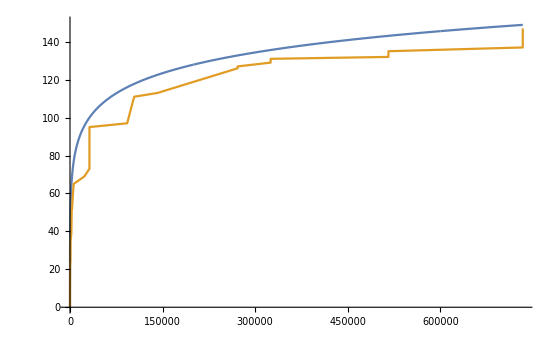

```mathematica
ListPlot[{Table[{n,Log[n]^(3/2)*3},{n,1,Max[1000,Max[First/@recordPoints]],25}],Select[recordPoints,True||First[#]<=1000&]},Joined->True,PlotRange->{0,150}]
```

Try fitting a logarithm or something to this line. Also try products of iterated logarithms and different powers. Huh, it would be great to get a continuous version of log^.bak(n), and moreover a continuous version of products of different numbers of those (where we make the “number of them” continuous—you can think of this as a monotonic map from the naturals into the reals (giving the iteration of each term), but then turn the naturals into the reals as well. Aaaaand...it’d be great to integrate this with powers of these logarithms (which includes powers of n ofc: iteration of log 0 times). Overambitious, I think. But not impossible?

```mathematica
E/2//N
```

1.35914

```mathematica
ApparentHeight[21,200]
```

2

```mathematica
ApparentHeight[5941,200]
```

65

```mathematica
E^2(5941)^(1/4)//N
```

64.8715

```mathematica
Total[%299]
```

Total[%299]

```mathematica
{12,13,13,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,22,22,22,22,22,22,24,24,24,24,36,43,44}//Length
```

41

```mathematica
E^2//N
```

7.38906

```mathematica
Table[ApparentHeight[n,25],{n,1,20}]
```

{0,1,1,2,1,2,1,2,3,3,2,2,1,2,5,3,3,2,2,3}

```mathematica
Clear[ApparentHeight]
```

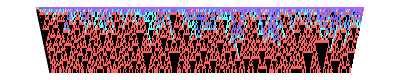

```mathematica
CreateDownwardTiling[300,25,G,PolygonGraphic[##,Text->False]&]//Graphics
```

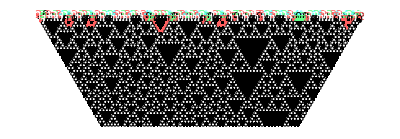

```mathematica
CreateDownwardTiling[100,40,GMod1[5],PolygonGraphic]//Graphics
```